```mathematica
p = ToExpression["(x_1)^4 + x_2^4 - 2/3", TeXForm]
```

-2/3+x_1^4+x_2^4

```mathematica
f = {{ToExpression["-1/4x_1^7-1/4x_1^3x_2^4+1/6x_1^3", TeXForm]},
{ToExpression["-1/4x_1^4x_2^3-1/4x_2^7+1/6x_2^3", TeXForm]}}
```

{{x_1^3/6-x_1^7/4-1/4 x_1^3 x_2^4},{x_2^3/6-1/4 x_1^4 x_2^3-x_2^7/4}}

```mathematica
h = {Subscript[x, 2]^3,-Subscript[x, 1]^3}
```

{x_2^3,-x_1^3}

```mathematica
f0 = f
```

{{x_1^3/6-x_1^7/4-1/4 x_1^3 x_2^4},{x_2^3/6-1/4 x_1^4 x_2^3-x_2^7/4}}

```mathematica
f0 // TeXForm
```

\left(
\begin{array}{c}
 -\frac{x_1^7}{4}-\frac{1}{4} x_2^4 x_1^3+\frac{x_1^3}{6} \\
 -\frac{x_2^7}{4}-\frac{1}{4} x_1^4 x_2^3+\frac{x_2^3}{6} \\
\end{array}
\right)

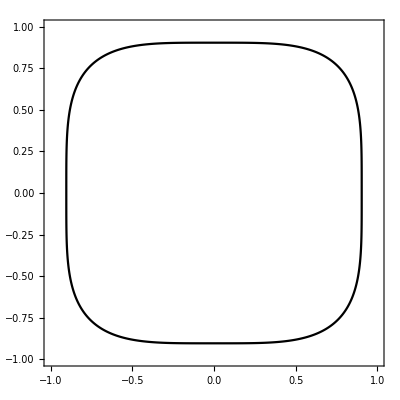

```mathematica
C1 = ContourPlot[p==0,{Subscript[x, 1],-1,1},{Subscript[x, 2],-1,1},ContourStyle-> Black,PlotPoints->100,MaxRecursion->2]
```

```mathematica
R = 1;
phi = {Subscript[x, 1]^3,Subscript[x, 1]^2*Subscript[x, 2],Subscript[x, 1]*Subscript[x, 2]^2,Subscript[x, 2]^3,Subscript[x, 1]^2,Subscript[x, 1]*Subscript[x, 2],Subscript[x, 2]^2,Subscript[x, 1],Subscript[x, 2],1};
dphi = {D[phi, Subscript[x, 1]], D[phi, Subscript[x, 2]]}
```

{{3 x_1^2,2 x_1 x_2,x_2^2,0,2 x_1,x_2,0,1,0,0},{0,x_1^2,2 x_1 x_2,3 x_2^2,0,x_1,2 x_2,0,1,0}}

```mathematica
w1 = {214.4939,-214.7813,212.2193,-198.5436,-23.7224,2.9950,-16.9918,-436.2886,514.7067, 0}
```

{214.494,-214.781,212.219,-198.544,-23.7224,2.995,-16.9918,-436.289,514.707,0}

```mathematica
mu = - 1/2 * R^-1 * Dot[h,  Dot[dphi, Transpose[w1]]]
```

1/2 (x_1^3 (514.707+2.995 x_1-214.781 x_1^2-33.9836 x_2+424.439 x_1 x_2-595.631 x_2^2)-x_2^3 (-436.289-47.4448 x_1+643.482 x_1^2+2.995 x_2-429.563 x_1 x_2+212.219 x_2^2))

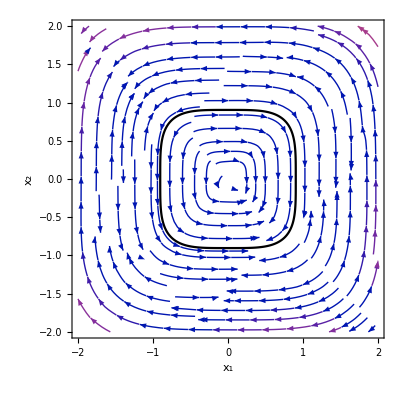

```mathematica
S1 = Show[StreamPlot[(f0 + h  * mu)[[;;, 1]],{Subscript[x, 1],-2,2},{Subscript[x, 2],-2,2}], C1,FrameLabel-> {Subscript[x, 1],Subscript[x, 2]}]
```